```mathematica
Plot3D[{x^2+x y + y^2,3},{x,-6,6},{y,-6,6} ]
```

```mathematica
f[x_, y_]=x^2+x y + y^2;Limit[(f[x+h, y]-f[x,y])/h,h->0]
```

2 x+y

```mathematica
D[(x^2+x y + y^2), x]
```

2 x+y

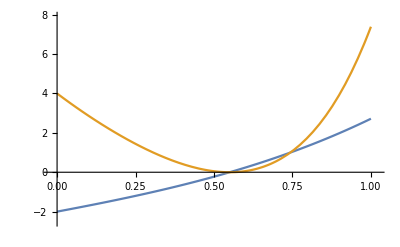

```mathematica
problem[x_]=x^3+2 x+E^x-3;error[x_]=problem[x]^2;Plot[{problem[x], error[x]},{x,0,1}]
```

```mathematica
D[((∑_(j=1)^m x^2+y+z) 1/m),x]
```

2 x

```mathematica
z = x^2+x y + y^2;D[z, x]
```

2 x+y

```mathematica
z = (a+1)(2a+b);{D[z, a],D[z, b]}
```

{2 a+2 (1+a)+b,1+a}

```mathematica
z=f[u,v];
u=g[x,y];
v=h[x,y];
(*
	∂_x z=∂_u z ∂_x u+∂_v z ∂_x v
∂_y z=∂_u z ∂_y u+∂_v z ∂_y v
*)
D[z, x]
```

f^(1,0)[g[x,y],h[x,y]] g^(1,0)[x,y]+f^(0,1)[g[x,y],h[x,y]] h^(1,0)[x,y]

```mathematica
Clear[x,y,z,u,v]
z=u^2+Sin[v];
u=x+y;
v =4 x-2y;
(*
	∂_x z = 2(x+y)+Cos[4x-2y]*4
∂_y z = 2(x+y)+Cos[4x-2y]*(-2)
*)
D[z, x] 
D[z, y]
```

2 (x+y)+4 Cos[4 x-2 y]

2 (x+y)-2 Cos[4 x-2 y]